Exam 2 Take-Home Project

In this project you will implement a code to simulate planetary motion. You will use the Runge-Kutta 2nd order method to integrate the equation of motion.

The project is organized into six tasks, through which you’ll develop a single program. 

TASK 1 (20 pts). First a quick analytical calculation to set up initial conditions for our problem. You’ll just need pen and paper and a calculator for this, and show your work in comments. 
We assume that the Sun is fixed at the origin (0,0) and that we know the perihelion and aphelion (Earth’s nearest and farthest point from the Sun respectively) to be 147.1 million km and 152.1 million km. Make an analytical calculation of what the Earth’s velocities are at these two points, v_1 and v_2. An exaggerated figure showing the elliptical orbit is shown below. The actual orbit is almost circular. You can solve it with two simple equations! Write down your steps in calculating v_1 and v_2 in the code as a comment, otherwise no points will be given. You’ll get to use  v_1 in Task 3.
Hint 1, Conservation of energy: Write down the total energy  = kinetic energy plus gravitational potential energy (-(G M m)/r) at the two points and equate them.
Hint 2, Conservation of angular momentum, a.k.a. Kepler’s Second Law: A line segment joining Earth and Sun sweeps out equal areas during equal intervals of time. Take a tiny sweep across an infinitesimally small time Δt near the perihelion and aphelion, and equate the areas (blue areas in figure). Δt will cancel out in the end.  You can look up the Solar mass and Gravitational Constant you need on Google. 
-Graphics-

TASK 2 (10 pts) What’s the characteristic timescale τ if you want to simulate the trajectory of Earth around the Sun? Describe how you use τ to determine an appropriate timestep dt for this simulation.

TASK 3 (10 pts). Initialize the Earth at the Perihelion with velocity v_1 pointing in the appropriate direction. It’s easiest to set up everything in SI units. Implement the expression for the gravitational force acting on the Earth F⃗ = -(G M m)/r^2 r̂= -(G M m)/r^3 r⃗ and the corresponding acceleration in the function diffeq(). Here r⃗ is the vector from the Sun to the Earth and r is its magnitude r=|r⃗|. 

TASK 4 (20 pts). Simulate the Earth’s trajectory for one year using Runge-Kutta 2nd order method. The resulting trajectory should be a closed orbit that passes through both the Perihelion and Aphelion.

TASK 5 (20 pts). Create a second plot to show the values of the energies (potential, kinetic, total) as a function of time. You can choose to plot this as a second subplot or in a separate figure.

TASK 6 (20 pts). Try to tweak Newton’s law of gravitation a little bit by changing the exponent of r in -(G M m)/r^3 r⃗ from –3 to –3.02. Simulate the Earth’s trajectory for 200 years. Describe what you see.

```mathematica
M=1.989 10^30;
G=6.6743 10^-11;
r1=147.1 10^9;
r2=152.1 10^9;
Solve[{
1/2 v1^2-(G M)/r1==1/2 v2^2-(G M)/r2,
r1 v1 == r2 v2},{v1,v2}]
```

{{v1→-30290.9,v2→-29295.2},{v1→30290.9,v2→29295.2}}

```mathematica
me = 6 10^24;
TE=1/2 me 30309^2-(G M me)/r1;
Lz=me 30309 r1;
Solve[(2 (TE-1/2 Lz^2/me/r^2+(G M me)/r))/me==0,r]
```

{{r→1.47×10^11},{r→1.52×10^11}}

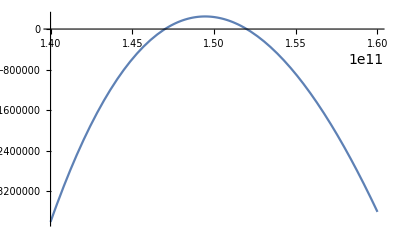

```mathematica
Plot[(2 (TE-1/2 Lz^2/me/r^2+(G M me)/r))/me,{r, 1.4 10^11,1.6 10^11}]
```

```mathematica
Plot[(2 (TE-1/2 Lz^2/me/r^2+(G M me)/r))/me,{r, 1.4 10^11,1.6 10^11}]
```

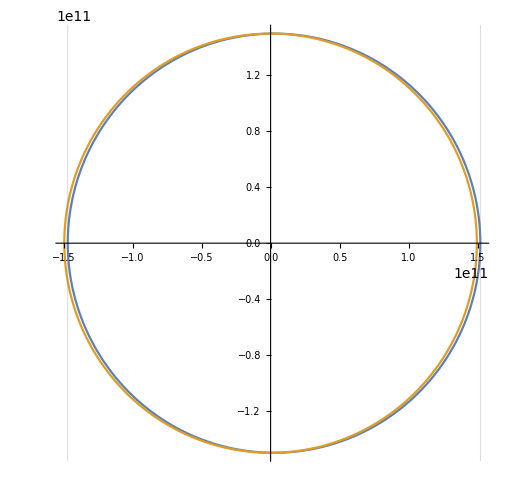

```mathematica
a=(r1+r2)/2;
f=(r2-r1)/2;
b=√(-f^2+a^2);
e=√(1-b^2/a^2);


PolarPlot[{(a (1-e^2))/(1-e Cos[t]),a},{t,0,2π},GridLines->{{-r1,r2},{}}]
```

```mathematica
Solve[a==(a (1.-e^2))/(1-e Cos[t]),t]
```

{{t→-1.55407},{t→1.55407}}